```mathematica
computeMarginals[table_]:=
{table⟦1⟧~Join~{Total[table⟦1⟧]},
table⟦2⟧~Join~{Total[table⟦2⟧]},
{Total[table⟦All,1⟧]}~Join~{Total[table⟦All,2⟧]}~Join~{Total[Total[table]]}}
```

```mathematica
computeP[contingencyTable_]:=
Module[{
R1=contingencyTable⟦1,3⟧,R2=contingencyTable⟦2,3⟧,
C1=contingencyTable⟦3,1⟧,C2=contingencyTable⟦3,2⟧,
N=contingencyTable⟦3,3⟧},
(R1!R2!C1!C2!)/(N!Times[Sequence@@(#!&/@Flatten[contingencyTable⟦;;2,;;2⟧])])]
```

```mathematica
createOutcomeSet[table_]:=
Drop[NestWhileList[{{#⟦1,1⟧-1,#⟦1,2⟧+1},{#⟦2,1⟧+1,#⟦2,2⟧-1}}&,
table,
MatrixQ[#,NonNegative]&
],-1]
```

```mathematica
createOutcomeSet2[table_]:=
Take[NestWhileList[{{#⟦1,1⟧+1,#⟦1,2⟧-1},{#⟦2,1⟧-1,#⟦2,2⟧+1}}&,
table,
MatrixQ[#,NonNegative]&
],{2,-2}]
```

```mathematica
fisherExactTestOneTail[table_]:=
Module[{res},
res={#,computeP[#]}&/@(computeMarginals/@(createOutcomeSet[table]));
Total[Select[res,#⟦2⟧≤res⟦1,2⟧&]⟦All,2⟧]
]
```

```mathematica
fisherExactTest[table_]:=
Module[{res},
res={#,computeP[#]}&/@(computeMarginals/@(createOutcomeSet[table]~Join~createOutcomeSet2[table]));
Total[Select[res,#⟦2⟧≤res⟦1,2⟧&]⟦All,2⟧]
]
```

```mathematica
testTwoConfigurations[succA_,succB_,num_]:=
fisherExactTest[{{num *succA/100,num *succB/100},
{num-num *succA/100,num-num *succB/100}
}]
```

```mathematica
testTwoConfigurations[77,86.4,500]//N
```

0.000158357

```mathematica
table={{44,63},{156,137}}
```

{{44,63},{156,137}}

```mathematica
fisherExactTest[table]//N
```

0.0417515

```mathematica
fisherExactTestOneTail[table]//N
```

0.0208758

```mathematica
MatrixForm/@Table[{{1,5},{i-1,i-5}},{i,5,12}]
```

{(1 | 5
4 | 0),(1 | 5
5 | 1),(1 | 5
6 | 2),(1 | 5
7 | 3),(1 | 5
8 | 4),(1 | 5
9 | 5),(1 | 5
10 | 6),(1 | 5
11 | 7)}

```mathematica
fisherExactTest/@Table[{{1,5},{i-1,i-5}},{i,5,12}]//N
```

{0.047619,0.0800866,0.102564,0.118881,0.131222,0.140867,0.148607,0.154953}

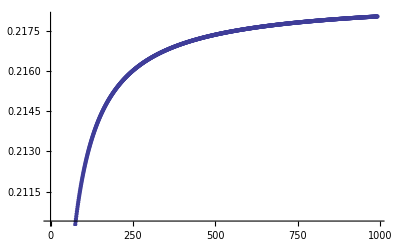

```mathematica
ListPlot[fisherExactTest/@Table[{{1,5},{i-1,i-5}},{i,10,1000}]]
```